```mathematica
(*zadanie1 pierwiastki*)
Solve[4x^2-3x-6==0,x]
```

{{x→1/8 (3-√105)},{x→1/8 (3+√105)}}

```mathematica
(*zadanie2*)
```

```mathematica
(*a)*)
Integrate[((x^2-a^2)^(3/2)/x^3),x]
```

(1+a^2/(2 x^2)) √(-a^2+x^2)+3/2 a ArcTan[a/(√(-a^2+x^2))]

```mathematica
(*b*)
Limit[(2n+1)/(3n+1),n->Infinity]
```

2/3

```mathematica
D[(1/5)x^5ArcTan[x]-(1/20)x^4+(1/10)x^2-(1/10)Log[1+x^2],{x,3}]
```

-(6 x)/5-(6 x^5)/((1+x^2)^2)+(12 x^3)/(1+x^2)+1/5 x^5 ((8 x^2)/((1+x^2)^3)-2/((1+x^2)^2))+1/10 (-(16 x^3)/((1+x^2)^3)+(12 x)/((1+x^2)^2))+12 x^2 ArcTan[x]

```mathematica
(*Zadanie 3*)
```

```mathematica
wyniki={}
```

{}

```mathematica
For[i=-4,i<5,i++,AppendTo[wyniki,5Sin[5i^2]]]
```

```mathematica
wyniki
```

{5 Sin[80],5 Sin[45],5 Sin[20],5 Sin[5],0,5 Sin[5],5 Sin[20],5 Sin[45],5 Sin[80],5 Sin[80],5 Sin[45],5 Sin[20],5 Sin[5],0,5 Sin[5],5 Sin[20],5 Sin[45],5 Sin[80]}

```mathematica
(*zadaniae 4*)
(*punktowy*)
```

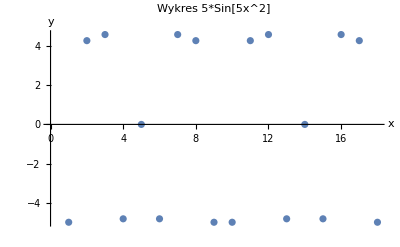

```mathematica
ListPlot[wyniki,AxesLabel->{x,y},PlotLabel->"Wykres 5*Sin[5x^2]"]
```

```mathematica
(*Liniowy*)
```

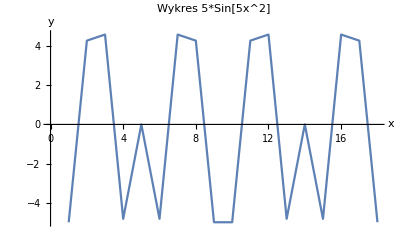

```mathematica
ListPlot[wyniki,Joined->True,AxesLabel->{x,y},PlotLabel->"Wykres 5*Sin[5x^2]"]
```

```mathematica
(*zadanie 5*)
```

```mathematica
Plot3D[Sin[2x]Cos[4y],{x,-2Pi,2Pi},{y,-2Pi,2Pi},Boxed->False,Mesh->None,Ticks->{{0,-2Pi,-Pi,Pi,2Pi},{0,-2Pi,-Pi,Pi,2Pi},{-1,0,1}}]
```

-Graphics3D-